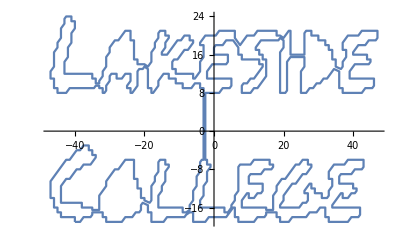

```mathematica
img0=Import["/home/michael/Downloads/Untitled drawing.jpg"];
img=Binarize[img0~ColorConvert~"Grayscale"~ImageResize~190~Blur~0,.15];
img=DeleteSmallComponents@img;
pts=DeleteDuplicates@Flatten[Cases[Normal@ListContourPlot[Reverse@ImageData[img],Contours->{0.5}],_Line,-1][[All,1]],1];
center=Mean@MinMax[pts]&/@Transpose@pts;
pts=#-center&/@pts;
shortest=Last@FindShortestTour@pts;
pts=pts[[shortest]];
ListLinePlot[pts]
```

```mathematica
SetAttributes[toPt,Listable]
toPt[z_]:=ComplexExpand[{Re@z,Im@z}]//Chop;
cf=Compile[{{z,_Complex,1}},Module[{n=Length@z},1/n*Table[Sum[z[[k]]*Exp[-I*i*k*2 Pi/n],{k,1,n}],{i,-m,m}]]];
z=pts[[All,1]]+I*pts[[All,2]];
m=100;
cn=cf[z];
cnjs = Table[{ Re[cn⟦i⟧],Im[cn⟦i⟧] },{i,1,Length[cn]}];
```

```mathematica
cnjs
```

{{-0.0499613,-0.0295971},{0.0904591,0.018737},{0.0131122,-0.02905},{0.0712603,0.0191605},{0.0582704,0.0300008},{-0.0320734,0.00806978},{-0.0742441,-0.0361257},{0.0189053,-0.0197824},{-0.0101888,-0.0548338},{-0.00570986,0.048545},{0.0787266,0.00327995},{-0.045237,0.00904014},{-0.0387265,-0.0309664},{0.0278926,-0.047207},{0.000354615,-0.0667412},{0.0388792,-0.0221956},{0.0920995,0.0802428},{-0.00958331,-0.0828501},{0.000149929,0.0459702},{-0.0780047,0.0701364},{0.0367119,-0.0816159},{-0.0767957,-0.00520182},{0.0475022,0.0140377},{0.0575601,-0.0160614},{-0.076219,-0.0185474},{0.0763343,0.0771924},{-0.0758138,-0.0428675},{-0.0182655,-0.0255889},{0.0730855,-0.0681197},{0.0385667,-0.0124239},{0.0399358,0.0155486},{-0.017169,0.0244148},{0.0139499,0.0270847},{-0.0624849,-0.00279026},{0.0675599,-0.047132},{0.0701538,0.0123793},{0.094078,0.0262363},{-0.131359,0.132317},{-0.0351374,0.0392076},{0.021273,-0.151488},{-0.114622,-0.108645},{0.232007,0.0399519},{-0.037332,-0.057766},{0.015536,0.155632},{-0.0736747,-0.230924},{-0.0957579,-0.128646},{-0.114241,-0.109727},{0.0204559,0.0285144},{-0.254052,-0.00164907},{0.111956,0.349937},{0.160195,-0.212078},{0.0791137,-0.129162},{-0.287259,0.0100217},{0.0457595,0.0513964},{0.107125,-0.0945444},{-0.0511692,0.206308},{0.100291,0.00703654},{-0.0829651,0.0642068},{-0.0647459,0.258385},{-0.136961,-0.377057},{0.0628608,-0.00121268},{-0.0111606,0.0273334},{-0.151828,-0.10471},{0.182789,0.189068},{-0.144343,0.128817},{0.257835,-0.207666},{-0.107961,-0.029337},{-0.14377,0.0241753},{-0.0233059,-0.0981028},{0.0332066,0.14263},{-0.0225584,-0.164517},{-0.0114462,-0.350434},{0.203905,-0.221906},{0.416326,0.373534},{0.597473,0.327363},{-0.277251,-0.110699},{-0.0251248,0.54663},{-0.225332,0.459258},{-0.919376,-0.284901},{0.359168,-0.0518109},{0.0733929,-0.440162},{-0.357077,0.914828},{0.0200755,0.414702},{0.00189296,-0.0814335},{-0.725301,-1.07094},{-1.00507,-0.284155},{0.0931144,-0.267761},{1.00859,-0.571121},{-0.121219,0.503334},{0.250708,0.941976},{0.168797,-0.845738},{-0.811419,-0.129241},{0.00852199,0.132537},{1.2242,-1.62542},{0.546524,0.902675},{-0.818283,2.65698},{-3.15774,1.23007},{-11.4312,-1.1528},{3.4482,5.34668},{-3.17328,3.18505},{1.05462,1.1707},{-12.7768,-19.2096},{3.31632,-6.4486},{-8.4646,1.27092},{-3.74226,-2.30209},{-3.60679,0.472227},{0.984982,-0.522101},{-0.535406,1.01786},{-0.392585,-0.524989},{0.212846,-0.81107},{0.202606,-0.333282},{-0.678578,0.216388},{0.0224834,0.405652},{-1.46015,-0.426646},{0.0362989,-0.343085},{0.431876,-0.43008},{-0.91952,-0.565633},{-0.355033,0.0536601},{0.429975,-0.199661},{0.460781,-0.660292},{-0.31788,-0.193184},{-0.376561,-0.310523},{0.46228,-0.636163},{0.428516,-0.0742903},{0.0772706,0.367493},{0.188973,-0.267392},{0.0272552,0.307952},{0.262744,-0.0621061},{-0.120742,-0.0590312},{-0.0529485,-0.275356},{-0.0624311,0.113935},{0.151656,0.156857},{0.333827,0.178019},{0.000453579,0.0077255},{0.152185,-0.0419116},{-0.140083,0.216774},{0.31022,0.364169},{-0.117958,-0.0000846841},{-0.200864,-0.0121912},{-0.0809278,0.118738},{-0.345869,-0.120389},{-0.0702088,-0.00680054},{0.274132,0.0291658},{0.283144,-0.0226479},{-0.156075,0.0581964},{0.197513,-0.27029},{-0.126388,0.192503},{-0.044087,-0.151177},{-0.293903,-0.0487118},{0.323428,0.315158},{0.0714429,-0.0985651},{0.235207,-0.123534},{-0.0803492,-0.0187239},{-0.0434373,-0.025154},{-0.0547615,-0.0157036},{-0.103305,-0.142326},{-0.0409947,-0.0969485},{0.102832,-0.0563236},{-0.057047,0.135629},{-0.0111659,-0.11936},{-0.0769904,0.0114718},{0.000116889,0.0710019},{0.0751275,-0.0557974},{-0.0448095,0.0817218},{-0.036799,0.142258},{-0.0417555,-0.0881672},{-0.0496549,-0.030646},{-0.0276813,-0.0461703},{0.0333511,-0.0443973},{0.0621926,0.07573},{-0.00141767,0.0717595},{-0.0893034,-0.0763226},{-0.0291752,0.0182441},{-0.0170146,-0.0798526},{0.0182012,-0.0193563},{0.00180391,0.0804224},{0.0269579,0.0284948},{0.000491703,-0.0231674},{-0.00859191,-0.0146538},{0.0229317,0.0182369},{-0.000726273,-0.05586},{0.0553093,0.018034},{0.023505,0.0264721},{0.00263912,0.00695009},{-0.00131217,0.0260774},{-0.0247176,0.046269},{-0.02493,-0.05581},{-0.0191551,-0.0275484},{0.0506526,-0.0012206},{0.00940327,0.0400034},{-0.0512328,0.058851},{0.00996112,0.0521},{0.00783339,-0.069185},{-0.0285433,-0.0352424},{0.0181184,0.0489989},{0.0430999,-0.0259688},{-0.0505494,0.0287772},{-0.0073016,0.0337011},{-0.0687635,-0.0304356},{-0.0396426,0.0425738},{0.0451943,0.0057725}}